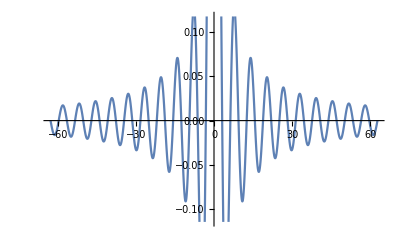

```mathematica
f[x_]:=Sin[x]/x
Plot[f[x],{x,-20Pi,20Pi}]
```

```mathematica
f[x_]:=3x^3+2x^2+x+5
g[x_]:=x^3
x={1,10,100,1000,1000000}
f[x]
N[f[x]/g[x],20]
```

{1,10,100,1000,1000000}

{11,3215,3020105,3002001005,3000002000001000005}

{11.,3.215,3.020105,3.002001005,3.000002000001000005}

```mathematica
NumberForm[0.5000033333500008,48]
```

0.5000033333500008

```mathematica
0.5000033333500008
```

```mathematica
Clear[x]
Limit[Sqrt[4x^2+1]-2x,{x->Infinity}]
```

{0}

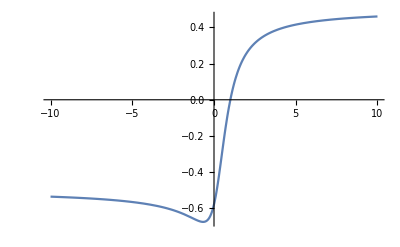

```mathematica
f[x_]:=(x-1)/Sqrt[4x^2-2x+3]
Plot[f[x],{x,-10,10}]
```

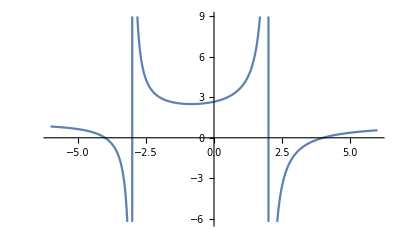

```mathematica
f[x_]:=(x^2-16)/(x^2+x-6)
Plot[f[x],{x,-6,6}]
```

```mathematica
(x+3)(x-2)//Expand//TraditionalForm
```

x^2+x-6